```mathematica
bifurcationPlot=f↦Module[
{
sign=D[f,x]>0
},
Show[
ContourPlot[If[sign,1,Null]f==0,{r,-3,3},{x,-3,3},ContourStyle->Dashed,FrameLabel->{"r","x^*"}],
ContourPlot[If[sign,Null,1]f==0,{r,-3,3},{x,-3,3}]
]
];
phasePlot=f↦Manipulate[
Module[{
sign=D[f,x]>0,
nodes=Select[#∈Reals&]@
(x/.Solve[f==0,x])
},
Plot[f,{x,-3,3},PlotRange->{-5,5},
Epilog->{
PointSize[Large],
Point[Map[{#,0}&]@Select[Not[sign/.(x->#)]&]@nodes],
Point[Map[{#,0}&]@Select[sign/.(x->#)&]@nodes],
White,
Point[Map[{#,0}&]@Select[sign/.(x->#)&]@nodes]
},AxesLabel->{"x", "dx/dt"}]
],
{r,-3,3}
];
```

```mathematica
r+x^2
```

r+x^2

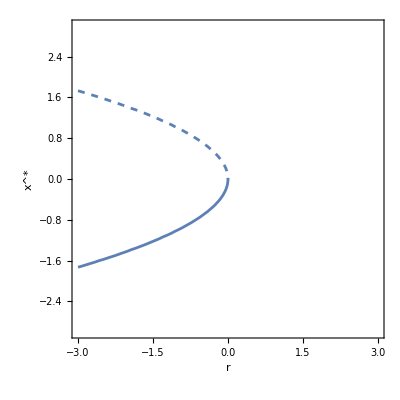

```mathematica
phasePlot[%]
bifurcationPlot[%%]
```

```mathematica
r x -x^2+h 
Manipulate[
bifurcationPlot[%],
{{h,0},0,3}
]
```

h+r x-x^2

```mathematica
-r x +h 
Manipulate[
bifurcationPlot[%],
{{h,0},0,3}
]
```

h-r x

```mathematica
a x - b (x + w)
Manipulate[
bifurcationPlot[%],
{{a,0},0,50},
{{b,0},0,50},
{{w,0},0,50}
]
```

a x-b (w+x)

$Aborted

-Graphics3D-

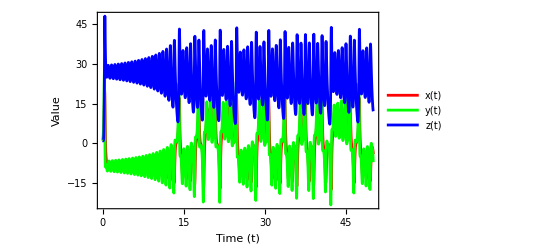

```mathematica
(*Lorenz System Parameters*)lorenzParameters={σ->10,ρ->28,β->8/3};

(*Lorenz System Equations*)
lorenzEquations={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]}/. lorenzParameters;

(*Initial Conditions*)
initialConditions={x[0]==1,y[0]==1,z[0]==1};

(*Solve the System*)
lorenzSolution=NDSolve[Join[lorenzEquations,initialConditions],{x,y,z},{t,0,50}];

(*Plot the 3D Trajectory*)
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. lorenzSolution],{t,0,50},PlotRange->All,AxesLabel->{"x","y","z"},PlotStyle->Blue,Boxed->True,LabelStyle->Directive[Bold,FontSize->14]]

(*Plot the Time Series for x,y,and z*)
Plot[Evaluate[{x[t],y[t],z[t]}/. lorenzSolution],{t,0,50},PlotLegends->{"x(t)","y(t)","z(t)"},Frame->True,FrameLabel->{"Time (t)","Value"},PlotStyle->{Red,Green,Blue},LabelStyle->Directive[Bold,FontSize->14]]
```